# Multi-Way Tag Systems in Coordinatized Rulial Space.

Dean Song Gladish

Carleton Class of 2020, mentor James Boyd @ WSS, 2022. 

These are lovely systems. Suppose we want infinite feedback and at the same time want the graph to continue on generating indefinitely.

Abstract.
To advance our understanding of computational irreducibility, my project studies the behavior of tag systems with different rules & initial conditions, evaluated as single-way rules and multi-way tag systems. My project focuses on comparing single-way and multi-way behavior, exploring explosive, degenerate, and cyclic behavior, and visualizing novel instances of the Ruliology. Generating analogues of Turing Machine Groups with multi-way tag systems, the work provides a new coordinatized method for studying the Ruliad and Rulial space.

What is the goal of the project? To look at single-element, then two-element spatial tag systems; for each, we can generate the multi-way graph starting from different initial conditions. To be much more analyzable, we do it extremely systematically starting with the single-character case. 

We look at all binary numbers 0, 1, 00, 01, 10, 11, 000, 001, etc. and remove the first digit for the initial conditions; for the rules, the same kind of thing. 

Regardless of whether the update is being put at the right hand of the string, this project is called a stag system because it’s about a spatial tag system; a system that can do its update from any point in space. As a result, we can visualize a multi-way tag system which increments depending on the value of the tag system rules, that depend on the rule cycle’s number of dimensions distributed by the cycle sequence that generates paths, generating explosive behavior when the tag system rules increase the string dimension. Most four-rule tag systems seem to be exploding. Because in Post’s tag system, that makes a large discrepancy in the length of tag system rules. 

If the rules are all mapping two length to three length then the tag systems are just always exploding. 

Tag System #1.

```mathematica
-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 0, 0}
```

## Section 1. Functions & Dependencies.

To properly and clearly describe the evolution of the Post Tag System, we implement Post’s ideas within the Wolfram Language Code. 

This section aims to describe ideas and arguments in a clear narrative format, to explain how Post’s tag system is studied and how the tag system becomes a Stag System in the Wolfram Language Code, using sections for each major step function or point of clarification/pivot.

### Subsection 1. Make Shifted Tag System with an Arbitrary Set of Rules.

The idea is to look at the evolution of tag systems across time yes, but how? With the implementation of Table with NestGraph, permitting the generation of graphs with layered di-graph embedding, portrays the evolution of new tag systems in the Wolfram Language Code.

Plot the time evolution of, for instance Tag System #2., for time steps i = 1, 2, ..., n.

```mathematica
Table[NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
i,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Automatic],
{i,1,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

For Tag System #2., Take a closer look and plot the nth time step with definition of MultiwayTagSystem.

```mathematica
MultiwayTagSystem[rule_,init_,t_]:=NestGraph[
rule,
init,
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Full
]
```

```mathematica
MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
8
]
```

-Graphics-

For Tag System #2., Plot the first few complements of the MultiwayTagSystem vertex list, providing the length of the complement.

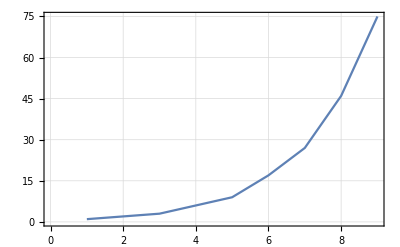

```mathematica
ListLinePlot[Table[
Length[
Complement[
VertexList[MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
t
]],
VertexList[MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
t-1
]]
]],
{t,2,10}
],
PlotTheme->"Detailed",
ImageSize->Automatic
]
```

For Tag System #2., Take the greater complement from time step t - 1 to time step t, for the MultiwayTagSystem function.

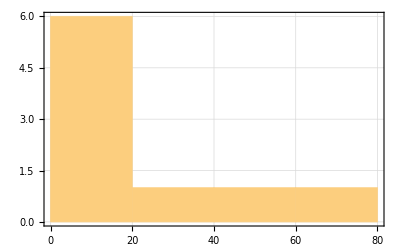

```mathematica
Histogram[
Table[
Length[
Complement[
VertexList[MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
t
]],
VertexList[MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
t-1
]]
]],
{t,2,10}],
5,
PlotTheme->"Detailed"
]
```

Instantiate the idea: Random Multi-way Tag Systems based on visualizing tag system possibilities in the form of a multi-way graph.

```mathematica
RandomMultiwayTagSystem[g_]:=Table[ArrayPlot[Reverse@Transpose[PadRight[With[
{
vertices=VertexList[g],randomInit=Table[RandomInteger[{0,1},3],8]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]][[i]],
{Automatic,Automatic},
.25]],
Frame->True,
ColorRules->{0->Hue[.95,.4,1.4],1->Hue[.1,.1,.1]},
Mesh->True],
{i,1,Length[VertexList[g]]}]
```

Tag System #3., Let’s generate all stag systems, with parameters for the rule {0,0,s___} -> {0, 0, 0}, {1,0,s___} -> {0, 1, 0}, {0,1,s___} -> {1, 0}, {1,1,s___} -> {1, 1, 1}, {1, 0, 1}.

```mathematica
generateAllDistributedStagSystem[
l1_,l2_,l3_,l4_,
i1R_,i2R_,i3R_,i4R_,
init_,
timeSteps_
]:=Table[
Labeled[NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},l1][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},l2][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},l3][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},l4][[i4]]}]
}],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},l1][[i1]],
"b"->Tuples[{0,1},l2][[i2]],
"c":>Tuples[{0,1},l3][[i3]],
"d":>Tuples[{0,1},l4][[i4]],
"e":>init
|>]
],
{t,1,timeSteps},
{i1, i1R[[1]],i1R[[2]]},
{i2,i2R[[1]],i2R[[2]]},
{i3,i3R[[1]],i3R[[2]]},
{i4,i4R[[1]],i4R[[2]]}]
```

```mathematica
generateAllDistributedStagSystem[
3,3,2,3,
{1,1},{3,3},{3,3},{1,8},
{1,0,1},
5
]
```

{{{{{-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1}}}}},{{{{-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1}}}}},{{{{-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1}}}}},{{{{-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1}}}}},{{{{-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{0, 1, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 0, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 0}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1}}}}}}

For Tag System #3, repurpose the code for RandomPathCanyons.
Create the random multi-way tag system from the beginning with the accompaniment of string templates.

```mathematica
generatePathCanyon[
rule1_,
rule2_,
rule3_,
rule4_,
init_,
timeSteps_
]:=Table[Labeled[NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,rule1}],
{left___,1,0,s___}:>Flatten[{left,s,rule2}],
{left___,0,1,s___}:>Flatten[{left,s,rule3}],
{left___,1,1,s___}:>Flatten[{left,s,rule4}]
}],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->rule1,
"b"->rule2,
"c":>rule3,
"d":>rule4,
"e":>init
|>]
],
{t,1,timeSteps}]
```

```mathematica
generatePathCanyon[
{0,0,0},
{0,1,0},
{1,0},
{1,1,1},
{1,0,1},
5
]
```

{-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 0}
{0,1,s___}->{1, 0}
{1,1,s___}->{1, 1, 1}
{1, 0, 1}}

Can we generate all list plots for Post’s Tag System? Yes.

```mathematica
ruleAllListStepPlotsInitialConditions[lengthInitialConditionR_,lastTimeStep_]:=
Table[ListStepPlot[Legended[FlattenAt[
 Table[
Style[Text[
With[
{
graph = NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
}],
{Tuples[{0,1},i][[j]]},
timeStep,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
},
Table[
Length /@FindShortestPath[graph,First[VertexList[graph]],VertexList[graph][[v]]],
{v,1,Length[VertexList[graph]]}
]
]]][[1]][[1]],
{timeStep,1,lastTimeStep}
]
,
{#}&/@Range[lastTimeStep]],Tuples[{0,1},i][[j]]]],
{i,lengthInitialConditionR[[1]],lengthInitialConditionR[[2]]},
{j,1,2^i}]
```

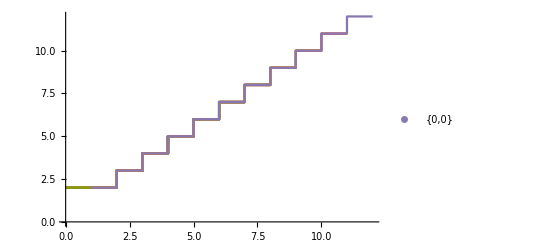
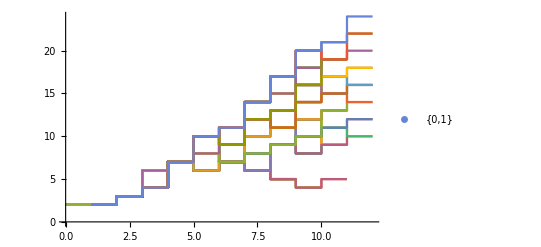
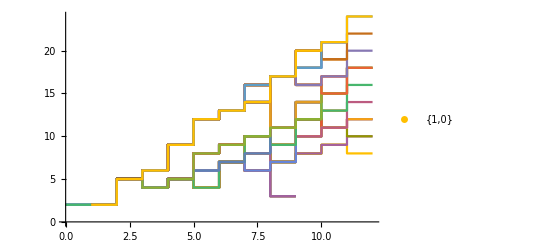
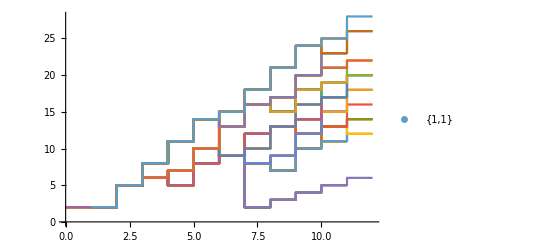
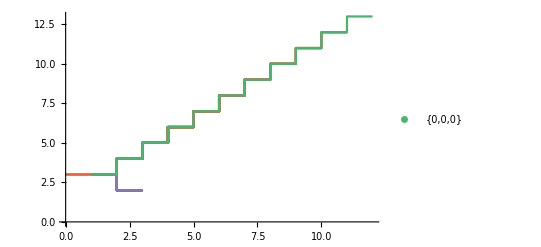
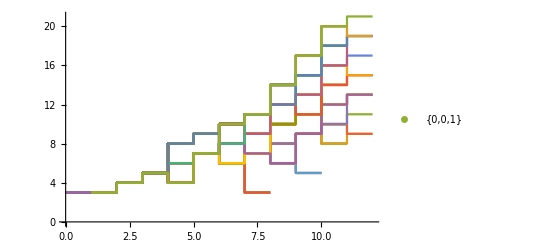
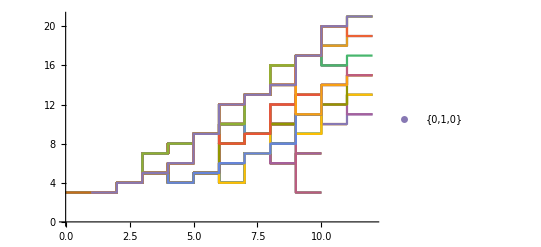
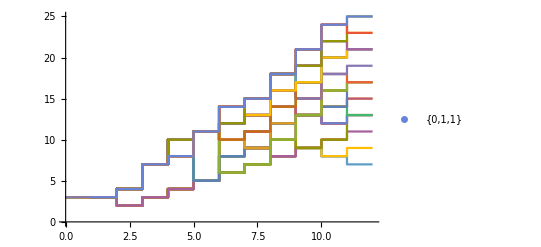

```mathematica
ruleAllListStepPlotsInitialConditions[{2,3}, 10]
```

The initial AllPathCanyonsBinary function, named because it finds the binary path of all path canyons like Tag System #2 @ Tuples[{0, 1}, 2][[2]].

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[Table[
Column[Row/@PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[j]],
{Automatic,Automatic},
.25
],Center]//. 0.25->"",
{j,2,Length[VertexList[g]]}
]//.{x_}:>x],FontFamily->"Roboto"]
```

```mathematica
Table[
AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,1,0,0}],
{left___,1,0,s___}:>Flatten[{left,s,0,1}],
{left___,0,1,s___}:>Flatten[{left,s,1,1,0}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},2][[i]]}]
}],
{{1,1}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]],
{i,1,4}
]
```

{{11
00,11
00
100,11
00
100
001,11
00
100
1100,11
00
100
001
0110,11
00
100
1100
0000,11
00
100
1100
1001,11
00
100
1100
11100,11
00
100
1100
0000
00100,11
00
100
001
0110
0101,11
00
100
001
0110
10110,11
00
100
1100
11100
10000,11
00
100
1100
11100
11001,11
00
100
1100
11100
111100},{11
01,11
01
110,11
01
110
001,11
01
110
101,11
01
110
001
0110,11
01
110
001
1100,11
01
110
101
1110,11
01
110
001
0110
0001,11
01
110
001
0110
0101,11
01
110
001
0110
10110,11
01
110
001
1100
1001,11
01
110
001
1100
11100,11
01
110
101
1110
1101},{11
10,11
10
01,11
10
01
110,11
10
01
110
010,11
10
01
110
101,11
10
01
110
010
001,11
10
01
110
010
0110,11
10
01
110
101
1110},{}}

The initial AllPathCanyons function, named because it finds the “generational” plots of binary tag systems.

```mathematica
AllPathCanyons[g_]:=Table[
ArrayPlot[
Reverse@Transpose[
PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[i]],
{Automatic,Automatic},
.25
]
],
Frame->True,
ColorRules->{0->Hue[.95,.4,1.4],
1->Hue[.1,.1,.1]},
Mesh->True
],
{i,1,Length[VertexList[g]]}
]
```

The initial AllPathCanyons function, applied to the “stag” system Tag System #1.

```mathematica
AllPathCanyons[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>{left,s,0,0,1},
{left___,1,0,s___}:>{left,s,0,0,1},
{left___,0,1,s___}:>{left,s,0,0,1},
{left___,1,1,s___}:>{left,s,0,0,1}}],
{{1,0,0}},
8,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
]
```

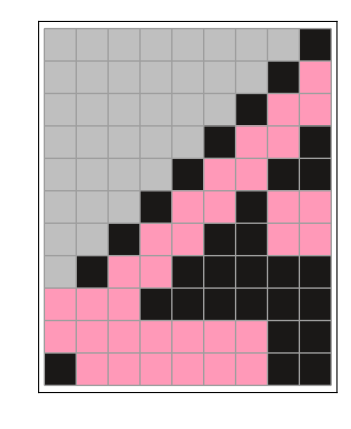
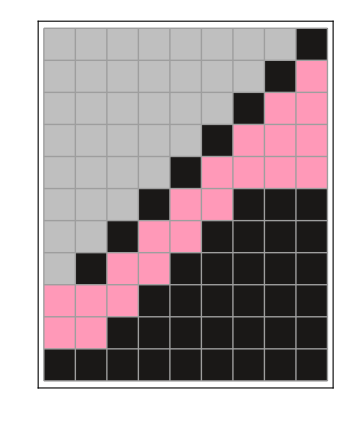
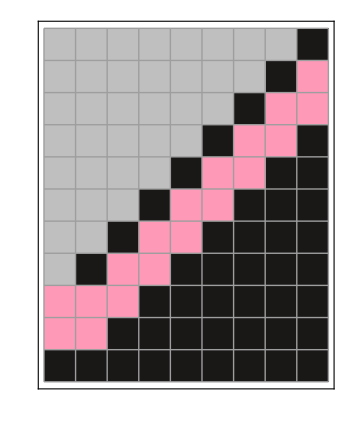

The Multi-Way NestGraph for Tag System #4.

```mathematica
g := With[{
g=NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},3][[5]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},2][[3]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},3][[1]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},2][[1]]}]}],{Tuples[{0,1},3][[1]]},3,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Large]},
Labeled[
HighlightGraph[
Graph[
g,
VertexLabels->Thread[VertexList[g]->(Length[#]&/@VertexList[g])]
],Style[PathGraph[FindShortestPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]]],DirectedEdges->True],Red]
],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},3][[5]],
"b"->Tuples[{0,1},2][[3]],
"c":>Tuples[{0,1},3][[1]],
"d":>Tuples[{0,1},2][[1]],
"e":>Tuples[{0,1},3][[1]]
|>]]]
g
```

-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{1, 0}
{0,1,s___}->{0, 0, 0}
{1,1,s___}->{0, 0}
{0, 0, 0}

### Subsection 2. The Temperature Plots with GraphDistanceMatrix.

The Temperature Plot of an initial condition for all Graph Distance Matrices.

```mathematica
generateAllTemperaturePlots[
l1_,l2_,l3_,l4_,
i1R_,i2R_,i3R_,i4R_,
init_,
timeSteps_,
branchialGraph_:True,
matrixForm_:True
]:=With[{
graph=NestGraph[ReplaceList[
{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},l1][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},l2][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},l3][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},l4][[i4]]}]
}
],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"]
},
Table[
{
Labeled[
ArrayPlot[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[graph]]/.∞->0,ColorFunction->"TemperatureMap", PlotLegends->Automatic],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},l1][[i1]],
"b"->Tuples[{0,1},l2][[i2]],
"c":>Tuples[{0,1},l3][[i3]],
"d":>Tuples[{0,1},l4][[i4]],
"e":>init
|>]],
If[branchialGraph,{{"[◼]", "BranchialGraph"}}[graph],Null],
If[matrixForm,Style[MatrixForm[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[graph]]],FontSize->8],Null]
},
{t,1,timeSteps},
{i1, i1R[[1]],i1R[[2]]},
{i2,i2R[[1]],i2R[[2]]},
{i3,i3R[[1]],i3R[[2]]},
{i4,i4R[[1]],i4R[[2]]}
] 
]
```

```mathematica
generateAllTemperaturePlots[
3,3,3,3,
{6,8},{4,4},{8,8},{4,4},
{1,1,0},
5,
True,
True
]
```

The Temperature Plot for Tag System #1.

```mathematica
generateOneTemperaturePlot[rule1_,rule2_,rule3_,rule4_,init_,timeSteps_,branchialGraph_:True,matrixForm_:True]:=With[
{
graph={{"[◼]", "BranchialGraph"}}[NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,rule1}],
{left___,1,0,s___}:>Flatten[{left,s,rule2}],
{left___,0,1,s___}:>Flatten[{left,s,rule3}],
{left___,1,1,s___}:>Flatten[{left,s,rule4}]
}],
{init},
timeSteps,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"]]
},
{
Labeled[
ArrayPlot[GraphDistanceMatrix[graph]/.∞->0,ColorFunction->"TemperatureMap", PlotLegends->Automatic],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->rule1,
"b"->rule2,
"c":>rule3,
"d":>rule4,
"e":>init
|>]],
If[branchialGraph,graph,Null],
If[matrixForm,Style[MatrixForm[GraphDistanceMatrix[graph]],FontSize->8],Null]
}]
```

```mathematica
generateOneTemperaturePlot[
{0,0,1},{0,0,1},{0,0,1},{0,0,1},
{1,0,0},
5,
False,
False
]
```

{-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 0, 0},Null,Null}

## Section 2. Descriptions of the Functions.

The AllPathCanyonsBinary function.

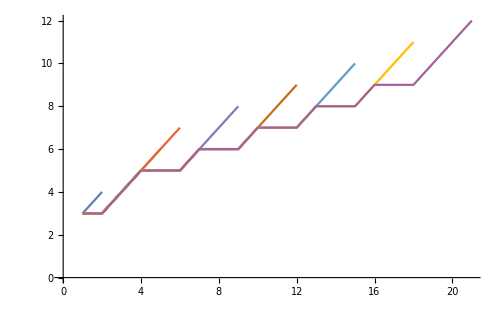
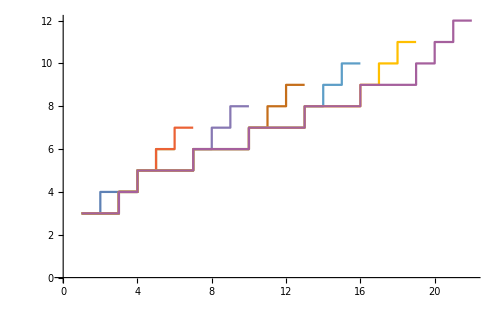
The AllPathCanyonsBinary function takes a multi-way graph and then graphically displays, much like the original multi-way tag systems plot with 0 and 1 as the constituents. The AllPathCanyonsBinary function is meant to take a NestGraph generated via multi-way tag system rule-set, and an initial condition and then provided the vertices of the given graph, revisits the FindPath function, or alternatively the FindShortestPath function, on the graph such that the first & last element of the vertex list function is taken all the way to Infinity, effectively finding all paths. Within the multi-way system, the AllPathCanyonsBinary function at all paths symbolically portrays all tag systems. 
-Graphics--Graphics-
The graphs represent the evolution of Tag System #6,
(0,0,s___) -> (0,1)
(1,0,s___)->(0,1,0)
(0,1,s___)->(1,0)
(1,1,s___)->(0,0,0)
(0,1,1)

```mathematica
The meaning is that as we time step from (1, 2, ..., n), we are plotting the length of the same tag system throughout n time steps with cyclic consequences. On the macro-level point, to explore the relationship between multi-way and single-way behavior, the interaction between multi-way and single-way behavior is that visualizing generational plots, named aptly because some of them are explosive, degenerate, and periodic, that some of these cycles depend on which path we take in the multi-way tag system. Because the function AllPathCanyons designs all tag systems at once, we can isolate single tag systems from the multi-way tag system graph and likewise the single tag systems from the ListStepPlot or ListLinePlots provided, allows us to visualize black and pink squares that represent 1 and 0 respectively, and that show the progression of a single-way tag system captured as a moment in the multi-way tag system graph vertex.
```

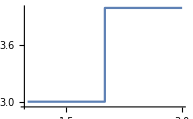
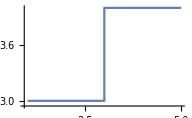
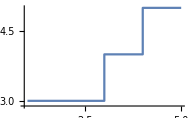
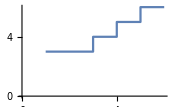
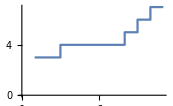
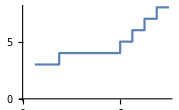
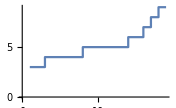
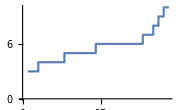

By bringing the ListStepPlot out of the nested tables we are able to plot them overlaid together, furthermore we are able to highlight all paths and shortest paths along the multi-way graph. We know that there are different single-way behaviors (explosive, degenerate, and periodic). Because the tag system above specifies a generally explosive single-way behavior across paths, visualizing explosive behavior in which the graph naturally tends to increment by a length of 1 but only when the conditions (1, 0) and (1, 1) are met somewhere in the string, since we can replace at any point in the string. Probably because our two-length tag system rules are manifesting cyclically, according to the three-length versus two-length tag system rules, we can specify tag systems that are explosive, or tag systems that are strictly incrementing.

The question is if any, what is the correspondence between single-way and multi-way behavior? The correspondence is that single-way behavior is manifested in each multi-way graph, if we follow the vertices.

## Section 3. Interesting Tag Systems.

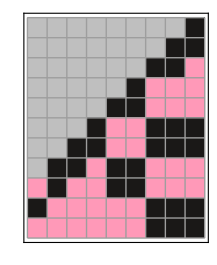
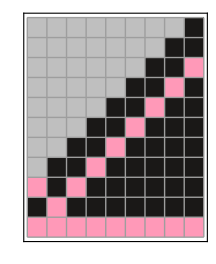
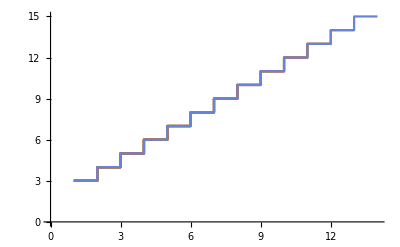
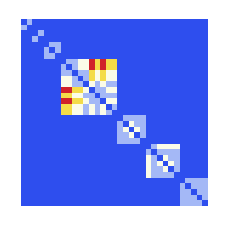
With regard to the implementation of the distance matrices, interesting is most nearly synonymous with the generation of cyclic behavior as seen on the graph distance matrix. Because our tag systems can be designed to create 4-cycles for instance, cycling through rules 1, 2, 3, and 4, we can generate interesting observed tag systems such as 

Tag System Example #7.
(0,  0) -> (0, 0, 1)
(1, 0) -> (0, 1, 1)
(0, 1) -> (0, 1, 1)
(1, 1) -> (0, 1, 1)
(0, 1, 0)

Leading to a checkerboard-like shape with accompanying ListLinePlot.

-Graphics--Graphics--Graphics-

The graph distance matrix describes, along the diagonal, the identity matrix for which blue indicates a distance of 0 or infinity. Whereas on the other hand, the graph distance matrix & branchial graph functions are colorizing the scale for 0, 1, ..., while values of 0 are ice cold and values of n roughly correspond to the time step n that is burning up. Let’s say we look at the 5th time step for the rules. It’s this tag system #1 which generates fractal-like tag system shapes which means that this tag system, selected for its resemblance to a chessboard, is one of the greatest tag systems of all time the reason being that the initial condition (0, 1, 0) leads to a layer of black color; 1s are being pushed further toward the top of the tag system which means that the (0, 0) -> (0, 0, 1) rule can be inserted at any location, right or left of the string allowing for untouched strings of (0, 0, 1) to be maintained, because in this single-way tag system 1s will simply pile up above (0, 0, 1). That is one of the most exciting relationships between single-way and multi-way behavior that has ever been seen, because even though we may not follow it all the way to the end of the branch, we definitely observe its pattern which occurs at ...0, 0,...

Tag System #8
(0, 0, s___) -> (1, 0)
(1, 0, s___) -> (0, 1, 1)
(0, 1, s___) -> (1, 1)
(1, 1, s___) -> (0, 0, 0)
(1, 1, 1)

-Graphics-

The values before the heat map are expressed in Matrix Form. 

(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 0 | 1 | 3 | 2 | 3 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 1 | 0 | 2 | 1 | 2 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 4 | 4 | 3 | 3 | 2 | 0 | 1 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 3 | 2 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 4 | 4 | 3 | 3 | 2 | 1 | 1 | 0 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 3 | 2 | 2 | 1 | 2 | 1 | 2 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 3 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 2 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 0 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 2 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 2 | 2 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 0 | 2 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 2 | 0 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 1 | 2 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 1 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 0)

Are all single-way paths in a multi-way system similar in behavior? The stag system #6
(0, 0) -> (0, 1)
(1, 0) -> (0, 1, 0)
(0, 1) -> (1, 0)
(1, 1) -> (0, 0, 0)
(0, 1, 1)
makes differential single-way paths.

-Graphics--Graphics--Graphics-

Tag System Example #2. 
(0,0,s___) -> (0, 1)
(1,0,s___) -> (0, 1, 0)
(0,1,s___ ) -> (1, 0)
(1,1,s___) -> (0, 0, 0)
(0, 1, 1)

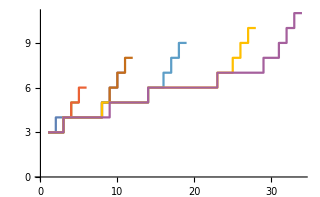
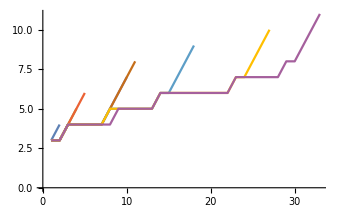

```mathematica
The ListStepPlot function, for which AllPathCanyonsBinary already records the length, has cyclic similarity in behavior in 4 steps.
```

Branchial graph for the tag system with 4-complete and 5-complete cycles.

```mathematica
{{"[◼]", "BranchialGraph"}}[NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,0,0,0}],
{left___,1,0,s___}:>Flatten[{left,s,0,0,0}],
{left___,0,1,s___}:>Flatten[{left,s,1,1}],
{left___,1,1,s___}:>Flatten[{left,s,1,0,1}]
}],
{{1,1,1}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]
```

-Graphics-

The partial state of completion shows the progression of nearly complete graphs in time steps, numerous disjoint sets which are “almost” 5-complete. 
{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 0, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 0}
-Graphics-
The idea is that there is only ever one zero supplied by the initial condition, the first tag system rule never gets invoked and for some reason we are still able to rotate around the last three rules, probably because all strings of two 1s or more can be re-written to generate three 1s while the section of the string that still has a 0 is shifted around with additional 1s at least from tag system rules {1,0,s___}->{0, 1, 1} and {0,1,s___}->{1, 0, 1}. The shortest path seems to be the one that is shifted around? 
-Graphics-

Multi-Way Graph for All Tag System Rules

```mathematica
Table[
Labeled[NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]
}],
{Tuples[{0,1},l][[k]]},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},j][[i1]],
"b"->Tuples[{0,1},j][[i2]],
"c":>Tuples[{0,1},j][[i3]],
"d":>Tuples[{0,1},j][[i4]],
"e":>Tuples[{0,1},l][[k]]
|>]
],
{t,1,10},
{i1,2^j,2^j},
{i2,2^j,2^j},
{i3,2^j,2^j},
{i4,2^j,2^j},
{j,3,3},
{k,2^l,2^l},
{l,3,3}]/.{{{{{{{x_}}}}}}} -> x
```

{-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1}}

Tag System Example #3.
(0,0,s___) -> (0, 0, 1)
(1,0,s___) -> (0, 0, 1)
(0,1,s___ ) -> (0, 0, 1)
(1,1,s___) -> (0, 0, 1)
(1, 0, 0)

-Graphics-

## Compare behaviors of different paths

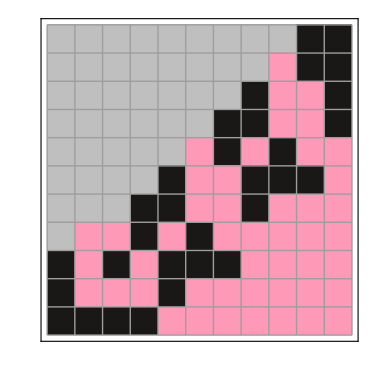
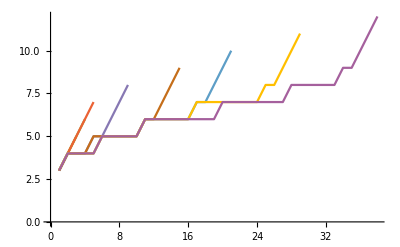
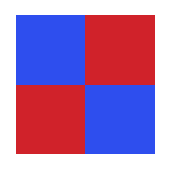
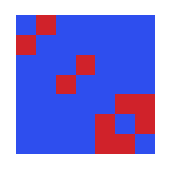
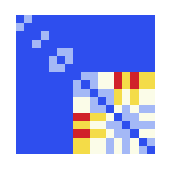
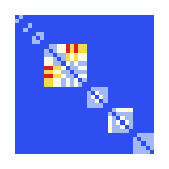
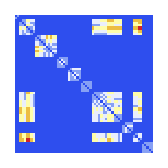
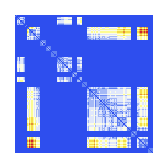
## Generation Plot Abiding by the rules (left___,0,0,s___) -> (left, s, 1,0) (left___,1,0,s___) -> (0,1,1) (left___,0,1,s___) -> (1,1) (left___,1,1,s___) ->{0,0,0) (1,1,1) we can derive explosive and straight paths. There are many behaviors to consider, because it’s a multi-way system at 10 steps. Portraying the effect of rule length 2, which transfers (left___, 0, 0, s___) to (left, s, 1, 0) and (left___, 0, 1, s___) to (left, s, 1, 1), when the paths are exploding they create (0, 1, 0) and (0, 0, 0) while when the paths are maintaining the same length they create the patterns (1, 0) and (1, 1). Focus on the new idea for tag systems, for which they can pick up the rules from anywhere in the string. Distributed, interior tag systems, also known as stag systems, are not really tag systems! In order to get something to decay, the (1, 0) for instance has to be shortened; in the Post tag system one is chopping off three at the beginning and either getting two added or four added, and that’s why it’s the marginal case. In the Post tag system, one is chopping off three at the beginning and either getting two added or four added, and the tag system is always going to explode because the length is always getting bigger. -Graphics- ListLinePlot of Lengths With the same tag system rule (Tag System Example #2 with initial condition (0,1,0)), (0, 0) -> (0, 1) (1, 0) -> (0, 1, 0) (0, 1) -> (1, 0) (1, 1) -> (0, 0, 0) It’s possible to find the shortest length path in terms of path length. For instance, the block of code Length /@ FindShortestPath[g, First[VertexList[g]], VertexList[g][[Length[VertexList[g]]]]] allows us to find the length array of the given tag system; and if we ant to find a longer array, then increase the number of time steps, inclusive of the first step. The finding for this one is that having a tag system comprised of different lengths for the initial rules results in a linearly increasing shortest path, to delineate nothing regarding paths that are perhaps longer and still produce explosive behavior in that cyclically, in four-step for our particular example, exhibits an explosion when the current string can only be rewritten with expansive rules (that is rules which rewrite the string to a higher dimension) and stalls flatly when the current string can only be rewritten with diminishing rules, that is rules which map greater lengths to equal or lesser lengths. Question: For time steps 1,2, ..., n, what does the tag system rule (0, 0) -> (0, 1) (1, 0) -> (0, 1, 0) (0, 1) -> (1, 0) (1, 1) -> (0, 0, 0) (0, 1, 0) look like in terms of our ListStepPlot function? -Graphics- State Transition Graphs GraphDistanceMatrix Array Plot Suppose we have the rule-set (0, 0, s___) -> (1, 0) (1, 0, s___) -> (0, 1, 1) (0, 1, s___) -> (1, 1) (1, 1, s___) -> (0, 0, 0) (1, 1, 1) -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics- Based on this example, it appears that the “tag system branches” are tangentially-related, the explosive nature of which is reflected in this graph. Let’s take a closer look. -Graphics- Depending on which branch you follow, your string might decrease in size or increase in size. These tag systems have similarity across the board, for instance the fact that our stratification is repeating like a fractal. On the temperature plots we are able to see the degree of similarity between tag systems, that is 0 across the first diagonal, while infinity is also treated as 0 for the sake of visualizing the degrees of similarity from 1 to 4. If we want to look at a partially permuted version of the previous tag system we can look at (0, 0) -> (1, 1, 1) (1, 0) -> (0, 0, 1) (0, 1) -> (1, 1, 0) (1, 1) -> (0, 1, 1) (0, 0, 1) which gives the following behavior.

{{{{{{{{-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{1, 1, 0}
{1,1,s___}->{0, 1, 1}
{0, 0, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{1, 1, 0}
{1,1,s___}->{0, 1, 1}
{0, 0, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{1, 1, 0}
{1,1,s___}->{0, 1, 1}
{0, 0, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{1, 1, 0}
{1,1,s___}->{0, 1, 1}
{0, 0, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{1, 1, 0}
{1,1,s___}->{0, 1, 1}
{0, 0, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{1, 1, 0}
{1,1,s___}->{0, 1, 1}
{0, 0, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{1, 1, 0}
{1,1,s___}->{0, 1, 1}
{0, 0, 1}}}}}}}}}

The behavior of this tag system is manifest in the branchial graph (and numerical adjacency matrix) for this graph, 
-Graphics-

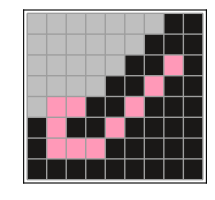
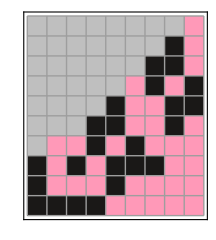
## Confluence To be quite honest, it’s questionable whether these multi-way graphs are confluent at all. The behavior of the multi-way graph for (0, 0) -> (1, 1, 1) (1, 0) -> (0, 0, 1) (0, 1) -> (1, 1, 0) (1, 1) -> (0, 1, 1) (0, 0, 1) is indicative of the multi-way evolution of tag systems for which, on the first branch for the third graph it is evident that there are two branches, because the first element is represented by (0, 0, 1) and thus can be converted either to (1, 1, 1) or to (0, 1, 1, 0), which is the rule specified by (0, 1, s___) -> (1, 1, 0). Once we have all those 1s, which can then be converted into (0, 1, 1) somewhere which adds the first 0, we are able to reconstruct all rules. In the event that either the tag system points toward coordinates with diminished dimensions, or the tag system is simply constructed such that only 1s are available, then, there could be degenerate behavior in that we might enter an extreme feedback loop. In this case we have (1, 1) -> (0, 1, 1) that prevents such a feedback loop from occurring. Likewise with the 0s except that perhaps there are other ways of forming a feedback loop that leads to degenerate tag system behavior. -Graphics-{0,0,s___}->{1, 1, 1} {1,0,s___}->{0, 0, 1} {0,1,s___}->{1, 1, 0} {1,1,s___}->{0, 1, 1} {0, 0, 1} Non-Cumulative Growth Rate (ListLinePlot and Histogram) (0, 0, s___) -> (1, 0) (1, 0, s___) -> (0, 1, 1) (0, 1, s___) -> (1, 1) (1, 1, s___) -> (0, 0, 0) (1, 1, 1) Multi-way behavior demonstrated does corroborate that varying length of the initial rules leads to explosive & periodic multi-way binary tag system re-writing. The only one of its kind? No. 111 1000 0011 001111 0111111 11111111 -Graphics- The observed behavior for this tag system could be that following the same sequence of multi-way steps allows patterns like -Graphics- patterns to keep repeating, because we are assigning (1, 1) to (0, 0, 0) and then assigning (1, 0) to (0, 1, 1) at any location in the string therefore the stag system allows us to visualize each reachable path which repeats on a small scale.

```mathematica
Branchial Graphs
```

Branchial graph for the tag system with 4-complete and 5-complete cycles.

```mathematica
g = NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,0,0,0},
{left___,1,0,s___}:>{left,s,0,1,0},
{left___,0,1,s___}:>{left,s,1,0},
{left___,1,1,s___}:>{left,s,1,1,1}
}],
{{1,0,1}},
6,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Full
,VertexLabels->Thread[VertexList[g]->(Length[#]&/@VertexList[g])]
]

Labeled[g,
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->{0,0,0},
"b"->{0,1,0},
"c":>{1,0},
"d":>{1,1,1},
"e":>{1,0,1}
|>]
]

HighlightGraph[g,Style[PathGraph[FindShortestPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]]],DirectedEdges->True],Red]]
```

-Graphics-

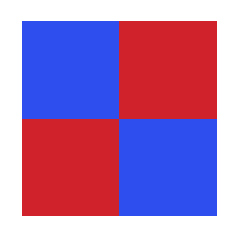
Tag System #6. 
{0,0,s___} -> {0, 0, 0}
{1,0,s___} -> {0, 1, 0}
{0,1,s___} -> {1, 0}
{1,1,s___} -> {1, 1, 1}
{1, 0, 1}
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
Even though we’re trying to generate a sequence of 111s, it seems that the multi-way tag system initial condition value of 1, 0, 1 allows the tag system to, due to the multi-way nature of the plots, alternatively push the existing 1s further up the graph with the application of the 0, 0 rule that is the first rule (once a second 0 is generated by {1,0,s___} -> {0, 1, 0}
{0,1,s___} -> {1, 0}) or combine the two into a staggered 0, 1, 0 or alternatively, 1, 0 plot in which we generate something that looks like a staircase... the multi-way characteristic is coming from the distributed stag system with left___.

## Concluding remarks

To summarize in conclusion, providing future plans & ideas for extension of the work, it would be brilliant to engage in further explorations of interesting tag system behavior. Whereas if we are implementing the tag system with different lengths for the rules, such as 
(0,0)->(0,1), (1,0)->(0,1,0), (0,1)->(1,0), and (1,1)->(0,0,0), it appears that the greatest factor in generating explosive behavior is variability in the initial conditions’ length. Applying this same tag system rule to the initial NestGraph which is the basis for our ListStepPlot in that we are taking the length of each path in the multi-way NestGraph, the shortest path from the initial state to the end state is the one in which the initial condition (0, 1, 0) is essentially inverted by the tag system. 
-Graphics-
The evidence suggests that the confluence of systems is consistent across permutations of tag systems. The multi-computational behavior mentioned is most evident via the alteration of initial rules, which can across our four and eight initial rules tend toward the degenerate forms, which typically do not arise due to the nature of string rewriting. 

The single-way behavior makes it clear that as long as the paths are connected in the branchial, adjacency matrix then they are related in the sense that they are able to continue without going into a self-destructive cycle of degeneracy. The meaning behind this is that this tag system, and the single-way behavior in the sense of tag system length, is likely to be regularly incremental. 

Question: What are some of the ways to reduce computational complexity such that we are able to compute these tag system rules across vast time steps? 

The initial condition as a proxy for its corresponding rules determines the shortest path, because the graph searches for the corresponding rules which may or may not include the absolute shortest path (absolute across the multi-way system).

## Keywords

Post Tag System

String Rewriting

Multi-Way & One-Way

## Acknowledgment

Props go to James for being such a kind mentor; and Stephen Wolfram defining the direction of this project toward methodically working upward. And to Post for providing the principal tag system.

## References

Mentor James Boyd, who teaches us keyboard shortcuts instead of Command + V. His passion (for entailment cones and) for multi-way computation in tag systems, and his insistence on having us meet with Nik, really kept things going.

Nik Murzin, whose generation of TwoWayMultiReplace has been nothing less than instrumental because he is the one who provides the scope and options for functions like TwoWayMultiReplace, with Identity, Uniquify, Canonicalize, and KeyMap Associations in .m nonetheless. Nik wrote things like Utilities, TwoWayRule, SubexpressionPositions, Rewriting, Quantifiers, MultiReplace, MultiCoReplace, MultiBiReplace, Metamathematics, Legacy, and Inference. He actually understands how the Mathematica kernel works!

Nik also does things like equational logic, axiomatic theory, and equation proof. When he is building the kernel, he builds things like Graph, LinkedHypergraph, Multicomputation, MulticomputationLoader, MulticomputationMain, MultiStringReplace, Utilities, and WFR. In fact, it is Nik who has created Tuples, HoldTuples, MatchSubstitutions. It’s so important for focusing on tag systems. It is Nik who has allowed the tag system rules to be applied anywhere in the current string.

Credit goes to Utkarsh for explaining how sequentality works so we didn’t think the past history had any bearing on the result of applying the tag system at any given time.